# Entregas de optimización

## Entrega 1

```mathematica
f[v_]:=100(v[[2]]-v[[1]])^2+(1-v[[1]])^2;
gradient[v_] :=Grad[f[x,y],{x,y}]/.{x->v[[1]],y->v[[2]]};
HessianH[f_,x_List?VectorQ]:=D[f,{x,2}];
```

```mathematica
lim = 5;
Plot3D[f[x1,x2],{x1,-lim,lim},{x2,-lim,lim},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
H =HessianH[100(x2-x1)^2+(1-x1)^2,{x1,x2}];
Inverse[H]//MatrixForm
H //MatrixForm
```

(1/2 | 1/2
1/2 | 101/200)

(202 | -200
-200 | 200)

```mathematica
D[100(x2-x1)^2+(1-x1)^2,{x2,1}]
```

200 (-x1+x2)

```mathematica
f[{2,5}]
Grad[f[x,y],{x,y}]
f[{2,5}-gradient[2,5]]
```

901

{-2 (1-x)-200 (-x+y),200 (-x+y)}

143161301

```mathematica
Grad[f[x,y],{x,y}]
```

{-2 (1-x)-200 (-x+y),200 (-x+y)}

## Entrega 2

```mathematica
Simplify[0.25(1-w)^2+0.3(1-w)w+0.10 w^2]
```

0.25-0.2 w+0.05 w^2

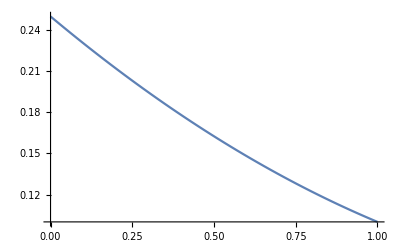

```mathematica
Plot[0.25-0.2 w+0.05000000000000002 w^2,{w,0,1}]
```